# Blatt 11, SS18 : Undulatorstrahlung

## Aufgabenstellung :

Berechnung des abgestrahlten Spektrums einer Ladung, die sich auf einem Kreis mit Radius R bewegt. 
Die Strahlungsleistung pro Frequenz- und Raumwinkelintervall berechnet sich zu

(d^2 I)/(dΩ dω)=A|∫_(-∞)^∞ (n(t)×{(n(t)-β(t))×β'(t)})/(1-β(t)·n(t))^2 e^(i ω (t - n(t)·r(t)/c))ⅆt|^2

Nur der zweite Term (Phasenterm) unter dem Integral hängt von der Frequenz ω ab.

### Die folgenden Zeilen müssen geändert werden da die Bahn im Undulator eine andere ist...

## Definitionen: Ladung auf der .......

Die Bahn liegt in der x-z Ebene, das ist der Ortsvektor als Funktion der Zeit.

```mathematica
(*//.{k-> (e B λu)/(2 π m c),βb-> 1-1/(2 γ^2) (1+k^2/2),ku-> (2 π)/λu}//FullSimplify*)
```

```mathematica
rvecfull[t_] = {k/(γ ku) Cos[ku βb c t],0,βb c t+k^2/(8 γ^2 ku) Sin[2 ku βb c t]}//FullSimplify
```

{(k Cos[c ku t βb])/(ku γ),0,c t βb+(k^2 Sin[2 c ku t βb])/(8 ku γ^2)}

Das ist β = v/c auf der Bahn... Geschwindigkeit durch γ ausgedrückt

```mathematica
βsync[t_] = D[rvecfull[t],t]/c
```

{-(k βb Sin[c ku t βb])/γ,0,(c βb+(c k^2 βb Cos[2 c ku t βb])/(4 γ^2))/c}

und das β’

```mathematica
βprime[t_] = Simplify[D[βsync[t],{t,1}]]
```

{-(c k ku βb^2 Cos[c ku t βb])/γ,0,-(c k^2 ku βb^2 Sin[2 c ku t βb])/(2 γ^2)}

Der Abstandsvektor (Beobachter - Ladung) sei raumfest. Dadurch geht man in des sogenannte Fernfeld. Dort ist die Verteilung der Strahlungsintensität nur noch vom Winkel abhängig, nicht von der aktuelle Koordinate. Wir beziehen den Winkel auf die Tangente an den Kreis bei t = 0. 
θ ist der Winkel den die Richtung zum Beobachter mit der Bahnebene bildet.

```mathematica
nvec = {Sin[ϕ]*Sin[θ],Cos[ϕ]*Sin[θ],Cos[θ]}
```

{Sin[θ] Sin[ϕ],Cos[ϕ] Sin[θ],Cos[θ]}

## Der erste Term ist ein Vektor, Zerlegung in π und σ Komponente

Der erste Faktor, der nicht von ω abhängt, mit raumfestem Abstandsvektor

```mathematica
fac1sync = FullSimplify[nvec×((nvec-βsync[t])×βprime[t])]/(1-βsync[t].nvec)^2 //.{βb-> 1-1/(2 γ^2) (1+k^2/2),ku-> (2 π)/λu}//FullSimplify
```

{(2 c k π (2+k^2-4 γ^2)^2 (Cos[(c π t (2+k^2-4 γ^2))/(2 γ^2 λu)] (16 γ^4 Cos[θ]^2+(2+k^2-4 γ^2) Cos[θ] (4 γ^2+k^2 Cos[(c π t (2+k^2-4 γ^2))/(γ^2 λu)])+16 γ^4 Cos[ϕ]^2 Sin[θ]^2)+2 k Sin[(c π t (2+k^2-4 γ^2))/(γ^2 λu)] (k (2+k^2-4 γ^2) Cos[θ] Sin[(c π t (2+k^2-4 γ^2))/(2 γ^2 λu)]+2 γ^3 Sin[2 θ] Sin[ϕ])))/(γ λu (16 γ^4+(2+k^2-4 γ^2) (Cos[θ] (4 γ^2+k^2 Cos[(c π t (2+k^2-4 γ^2))/(γ^2 λu)])+4 k γ Sin[θ] Sin[(c π t (2+k^2-4 γ^2))/(2 γ^2 λu)] Sin[ϕ]))^2),(16 c k π γ^2 (2+k^2-4 γ^2)^2 Cos[ϕ] Sin[θ] (k Cos[θ] Sin[(c π t (2+k^2-4 γ^2))/(γ^2 λu)]-2 γ Cos[(c π t (2+k^2-4 γ^2))/(2 γ^2 λu)] Sin[θ] Sin[ϕ]))/(λu (16 γ^4+(2+k^2-4 γ^2) (Cos[θ] (4 γ^2+k^2 Cos[(c π t (2+k^2-4 γ^2))/(γ^2 λu)])+4 k γ Sin[θ] Sin[(c π t (2+k^2-4 γ^2))/(2 γ^2 λu)] Sin[ϕ]))^2),(4 c k π (2+k^2-4 γ^2)^2 Sin[θ] (-4 k γ^3 Sin[θ] Sin[(c π t (2+k^2-4 γ^2))/(γ^2 λu)]+1/2 Cos[(c π t (2+k^2-4 γ^2))/(2 γ^2 λu)] (-16 γ^4 Cos[θ]+(2+k^2-4 γ^2) (-2 k^2-4 γ^2+k^2 Cos[(c π t (2+k^2-4 γ^2))/(γ^2 λu)])) Sin[ϕ]))/(γ λu (16 γ^4+(2+k^2-4 γ^2) (Cos[θ] (4 γ^2+k^2 Cos[(c π t (2+k^2-4 γ^2))/(γ^2 λu)])+4 k γ Sin[θ] Sin[(c π t (2+k^2-4 γ^2))/(2 γ^2 λu)] Sin[ϕ]))^2)}

```mathematica
fac1sync /. θ->0//FullSimplify
```

{(2 c k π (2+k^2-4 γ^2)^2 Cos[(c π t (2+k^2-4 γ^2))/(2 γ^2 λu)] (8 γ^2+2 k^2 (2+k^2-2 γ^2)-k^2 (2+k^2-4 γ^2) Cos[(c π t (2+k^2-4 γ^2))/(γ^2 λu)]))/(γ λu (4 (2+k^2) γ^2+k^2 (2+k^2-4 γ^2) Cos[(c π t (2+k^2-4 γ^2))/(γ^2 λu)])^2),0,0}

In der Bahnebene gibt es nur die x - Komponenten, das nennt man die σ - Polarisation.

```mathematica
ff1sigma= FullSimplify[fac1sync[[1]],{c>0,γ>1,t∈ Reals,R>0,0<θ<π}]
```

(2 c k π (2+k^2-4 γ^2)^2 (Cos[(c π t (2+k^2-4 γ^2))/(2 γ^2 λu)] (16 γ^4 Cos[θ]^2+(2+k^2-4 γ^2) Cos[θ] (4 γ^2+k^2 Cos[(c π t (2+k^2-4 γ^2))/(γ^2 λu)])+16 γ^4 Cos[ϕ]^2 Sin[θ]^2)+2 k Sin[(c π t (2+k^2-4 γ^2))/(γ^2 λu)] (k (2+k^2-4 γ^2) Cos[θ] Sin[(c π t (2+k^2-4 γ^2))/(2 γ^2 λu)]+2 γ^3 Sin[2 θ] Sin[ϕ])))/(γ λu (16 γ^4+(2+k^2-4 γ^2) (Cos[θ] (4 γ^2+k^2 Cos[(c π t (2+k^2-4 γ^2))/(γ^2 λu)])+4 k γ Sin[θ] Sin[(c π t (2+k^2-4 γ^2))/(2 γ^2 λu)] Sin[ϕ]))^2)

Für θ≠0  gibt es sowohl eine "y" als auch eine "z" Komponente, das muss aber so sein da der E-Vektor senkrecht auf n stehen muss.. Man sieht es wenn man das Verhältnis der Komponenten bildet :

```mathematica
fac1sync[[3]]/fac1sync[[2]]//FullSimplify
```

(Sec[ϕ] (-4 k γ^3 Sin[θ] Sin[(c π t (2+k^2-4 γ^2))/(γ^2 λu)]+1/2 Cos[(c π t (2+k^2-4 γ^2))/(2 γ^2 λu)] (-16 γ^4 Cos[θ]+(2+k^2-4 γ^2) (-2 k^2-4 γ^2+k^2 Cos[(c π t (2+k^2-4 γ^2))/(γ^2 λu)])) Sin[ϕ]))/(4 γ^3 (k Cos[θ] Sin[(c π t (2+k^2-4 γ^2))/(γ^2 λu)]-2 γ Cos[(c π t (2+k^2-4 γ^2))/(2 γ^2 λu)] Sin[θ] Sin[ϕ]))

oder einfach das Skalarprodukt

```mathematica
fac1sync.nvec//FullSimplify
```

0

Diese Komponente ist die π- Polarisation (senkrecht zur Bahnebene):

```mathematica
ff1pi =fac1sync[[2]]/Cos[θ]//FullSimplify
```

(16 c k π γ^2 (2+k^2-4 γ^2)^2 Cos[ϕ] Sin[θ] (k Sin[(c π t (2+k^2-4 γ^2))/(γ^2 λu)]-2 γ Cos[(c π t (2+k^2-4 γ^2))/(2 γ^2 λu)] Sin[ϕ] Tan[θ]))/(λu (16 γ^4+(2+k^2-4 γ^2) (Cos[θ] (4 γ^2+k^2 Cos[(c π t (2+k^2-4 γ^2))/(γ^2 λu)])+4 k γ Sin[θ] Sin[(c π t (2+k^2-4 γ^2))/(2 γ^2 λu)] Sin[ϕ]))^2)

sie verschwindet wie gesagt in der Bahnebene...

## Vorüberlegungen zum benötigten Zeitbereich für die Integration

Ist hier nicht notwendig, der Zeitbereich ist durch die Länge des Undulators gegeben.

## Der zweite Faktor, oder auch 'Phasenterm'

```mathematica
fac2 = FullSimplify[Exp[I ω(t - nvec.rvecfull[t]/c)]//.{βb-> 1-1/(2 γ^2) (1+k^2/2),ku-> (2 π)/λu}]
```

ⅇ^(-(ⅈ ω (-Cos[θ] (4 c π t (2+k^2-4 γ^2)+k^2 λu Sin[(c π t (2+k^2-4 γ^2))/(γ^2 λu)])+8 γ (-2 c π t γ+k λu Cos[(c π t (2+k^2-4 γ^2))/(2 γ^2 λu)] Sin[θ] Sin[ϕ])))/(16 c π γ^2))

## Das Modul zur Berechnung des abgestrahlten Spektrums

Ich lasse hier mal das Modul für die "Dipolstrahlung" als Muster stehen.  Die neuen Parameter sind jetzt :

Parameter : 
    xmin, xmax  : Frequenzbereich in Einheiten der Grundharmonischen
   nfp : Anzahl der Frequenzpunke
   θ und ϕ sind die Winkel
   K = Undulatorparameter
   energy = Elektronenstrahlenergie
   λu = Undulatorperiode
   nper : Anzahl der Undulatorperioden

Daraus dann jetzt also das neue "Module" oder "Block" basteln ....

```mathematica
Options[makeSRarc]={normspec->"normiert",ωrange->{0.01,5.},ωpoints->200,kpar->1.,energy->3.,undper->0.05,nper-> 1, logInterval->True};
```

```mathematica
makeSRarc[θin_,ϕin_,OptionsPattern[]] := 
Block[{λu,k,np,β,mc=3.*10^8,fac1,tmin,tmax,tstep,hquer= 1.05*10^-34,evolt= 1.6*10^-19,c=3.*10^8,γ,npoints,xmin,xmax,xfac,xlist,ωmax,ωres,facpi,facsigma,
tabpi,tabsigma,tabpiX,tabsigmaX,x,tab2,outlist,θ,ϕ,λ0},
θ=θin; (* warum man diese Ersetzung machen muss habe ich ausführlich erklärt. Funktionsargumente werden nur nach "Position" übergeben (slot1, slot2...) nicht nach Namen.*)
ϕ=ϕin;
γ = OptionValue[energy]/(0.511)*10^3;
β = √(1-1/γ^2);
λu = OptionValue[undper];
k=OptionValue[kpar];
np=OptionValue[nper];
tmin = 0;
tmax = (λu np)/((1-1/(2 γ^2) (1+k^2/2)) c);
tstep = tmax/1500; (* 1500 Punkte auf der Zeitachse *)
npoints =OptionValue[ωpoints];
xmin =  OptionValue[ωrange][[1]];
xmax =  OptionValue[ωrange][[2]];
xfac = (xmax/xmin)^(1/(npoints-1)); (* mir ist eine log Unterteilung für die Frequenz lieber *)

If[OptionValue[logInterval],xlist = Table[xmin*xfac^(n-1),{n,1,npoints}], xlist = Table[xmin+n*(xmax-xmin)/npoints, {n, 1, npoints}]]; 
ωmax = 1/tstep;
λ0=λu/(2 γ^2) (1+k^2/2+γ^2 θ^2);
ωres = 2 π c/λ0;

(* als erstes berechnen wir die Faktoren die nicht von ω abhängen *)
facsigma =Evaluate[ff1sigma];(* durch das "Evaluate" werden alle Zahlenwerte eingesetzt *) 
facpi = Evaluate[ff1pi];
tabpi = Table[facpi  ,{t,tmin,tmax,tstep}];
tabsigma = Table[facsigma  ,{t,tmin,tmax,tstep}];

outlist=Array[0&,Length[xlist]];
(* jetzt kommt der Loop über die Frequenzen. "x" ist ω/Subscript[ω, res] *)
Do[
x = xlist[[n]];
(* wir berechnen den Phasenterm auf dem gleichen Zeitraster *)
tab2 = Table[Evaluate[fac2//. ω->x ωres],{t,tmin,tmax,tstep}];
(* und das Produkt Phasenterm * Vorfaktor. Das wird automatisch elementweise gemacht *)
tabpiX = tabpi*tab2;
tabsigmaX = tabsigma*tab2;
(* das mit dem "Switch" ist die Feder auf dem Hut, man wählt damit ja nur die Einheiten aus. Das Integrieren wird einfach mit "Total" gemacht. *)
Switch[OptionValue[normspec],
"normiert",outlist[[n]]={x,θ,Abs[Total[tabpiX]*tstep]^2,Abs[Total[tabsigmaX]*tstep]^2},
"real",outlist[[n]]= {x ωres/(2π 10^15),θ,Abs[Total[tabpiX]*tstep]^2,Abs[Total[tabsigmaX]*tstep]^2},
"Energie",outlist[[n]] = {x*ωres*hquer/evolt,θ,Abs[Total[tabpiX]*tstep]^2,Abs[Total[tabsigmaX]*tstep]^2},
"Wellenlänge",outlist[[n]] =With[{λ =300./(x ωres/(2π 10^12)) }, {λ,ϕ,1/λ^2 Abs[Total[tabpiX]*tstep]^2,1/λ^2 Abs[Total[tabsigmaX]*tstep]^2}]],
{n,1,Length[xlist]}];
(*Print["f_c, λ_c    ",ωres/(2π 10^12),"  ",300.*2π 10^12/ωres];*)
Return[Drop[outlist,1]];
]
```

## Ergebnisse

```mathematica
test=makeSRarc[0.,0.,{normspec->"normiert",nper->2}];//Timing
```

{0.168,Null}

```mathematica
test[[1]]
```

{0.0103172,0.,0.,7690.56}

```mathematica
setnper=makeSRarc[0.,0.,{ωrange->{0.7,1.3},nper-> #}]&/@Range[10];
```

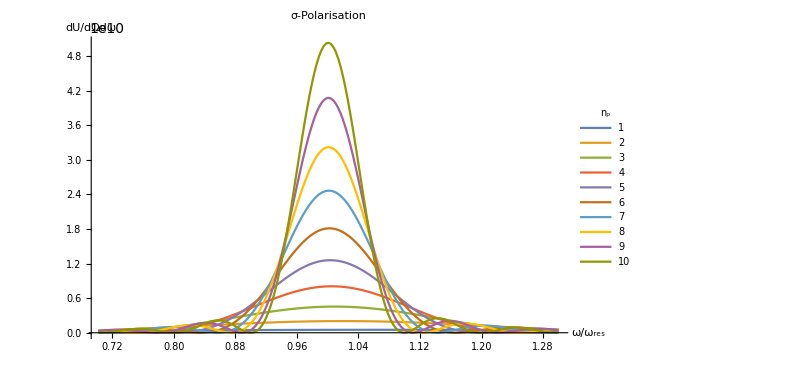

```mathematica
ListPlot[setnper[[All,All,{1,4}]], PlotRange->{All,All}, Joined->True,ImageSize->600, AxesLabel->{"ω/ω_res","dU/dΩdω"}, PlotLegends->LineLegend[Range[10], LegendLabel->"n_p"], PlotLabel->"σ-Polarisation"]
```

Das Spektrum hat den erwarteten sinc-förmigen Verlauf, ab n_p≃6 sieht man ihn deutlich. Dieser Verlauf entsteht durch Interferenz der aufgrund der Undulatorbewegung in leicht unterschiedliche Richtungen emittierten Strahlung.

```mathematica
setkpar=makeSRarc[0.,0.,{ωrange-> {0.00000001,20},ωpoints-> 1000,kpar-> #}]&/@{0.2,1,5};
```

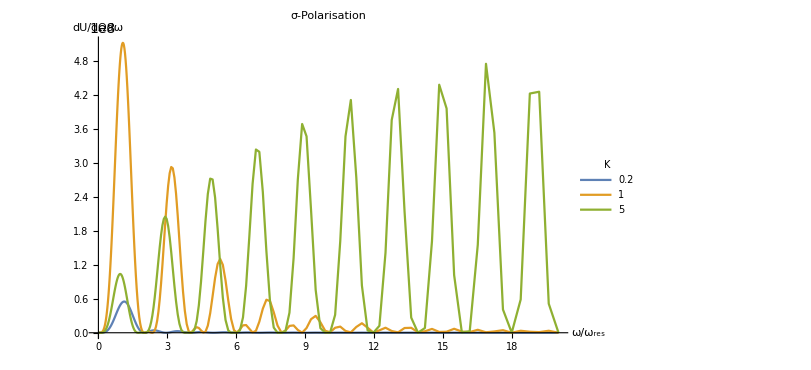

```mathematica
ListPlot[setkpar[[All,All,{1,4}]], PlotRange->{All,All}, Joined->True,ImageSize->600, AxesLabel->{"ω/ω_res","dU/dΩdω"}, PlotLegends->LineLegend[{0.2,1,5}, LegendLabel->"K"], PlotLabel->"σ-Polarisation"]
```

Für große K wird die Ablenkung so groß, dass keine Interferenz mehr auftritt, wodurch die höheren harmonischen nicht unterdrückt werden. Der Undulator wird nun als Wiggler bezeichnet.

```mathematica
Manipulate[ListPlot[makeSRarc[θ,0.,{ωrange-> {1,30},ωpoints->29,kpar-> k, logInterval->False}][[All,{1,4}]], PlotRange->{All,All}, ImageSize->600, AxesLabel->{"ω/ω_res","dU/dΩdω"}, PlotLegends->LineLegend[{k}, LegendLabel->"K"], PlotLabel->"σ-Polarisation"],{θ,0,π/1000},{k,0,5}]
```

Bei θ=0 ist die Verteilung der Intensität auf die harmonischen interessant. Die der ungeradzahligen harmonischen nimmt etwa sinc-förmig ab, während die geradzahligen niedrigen harmonischen praktisch verschwinden, aber man bei höheren ein lokales Maximum ist. Die Lage der Maxima verschiebt sich mit steigendem K nach rechts.

Die Intensität nimmt schon bei kleinen Winkelabweichungen rapide ab.

```mathematica
irel[n_,k_]:=n^2 (BesselJ[(n-1)/2,(k^2 n)/(4 (k^2/2+1))]-BesselJ[(n+1)/2,(k^2 n)/(4 (k^2/2+1))])^2
```

Vergleiche die Intensiäteten zwischen der 3. und 1. harmonischen

```mathematica
makeSRarc[0.,0.,{ωrange-> {1,30},ωpoints->31}][[3,4]]/makeSRarc[0.,0.,{ωrange-> {1,30},ωpoints->31}][[1,4]]
```

0.593577

```mathematica
irel[3,1]//N
```

0.403216

Vergleiche die Intensiäteten zwischen der 5. und 1. harmonischen

```mathematica
makeSRarc[0.,0.,{ωrange-> {1,30},ωpoints->31}][[5,4]]/makeSRarc[0.,0.,{ωrange-> {1,30},ωpoints->31}][[1,4]]
```

0.0626071

Irgendwie kommt uns da was komisch vor. Für n=1 sollte irel ja 1 ergeben

```mathematica
irel[1,1.]//N
```

0.828142

tut’s aber nicht. Irgendwo muss ein Fehler sein,

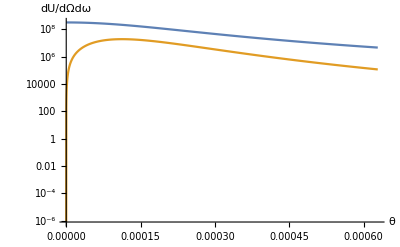

```mathematica
LogPlot[{makeSRarc[θ,0.,{ωrange->{1,5},ωpoints->6}][[1,4]],makeSRarc[θ,0.,{ωrange->{1,5},ωpoints->6}][[1,3]]}, {θ, 0, π/5000},PlotRange->{All,All}, AxesLabel->{"θ","dU/dΩdω"}]
```

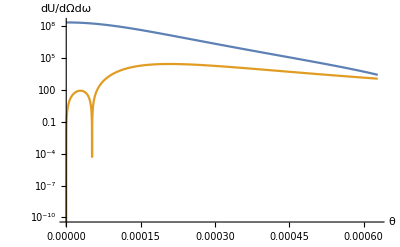

```mathematica
LogPlot[{makeSRarc[θ,0.,{ωrange->{1,6},ωpoints->6}][[3,4]],makeSRarc[θ,0.,{ωrange->{1,6},ωpoints->6}][[3,3]]}, {θ, 0, π/5000},PlotRange->{All,All}, AxesLabel->{"θ","dU/dΩdω"}]
```

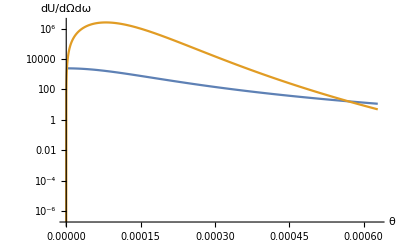

```mathematica
LogPlot[{makeSRarc[θ,0.,{ωrange->{1,6},ωpoints->6}][[5,4]],makeSRarc[θ,0.,{ωrange->{1,6},ωpoints->6}][[5,3]]}, {θ, 0, π/5000},PlotRange->{All,All}, AxesLabel->{"θ","dU/dΩdω"}]
```

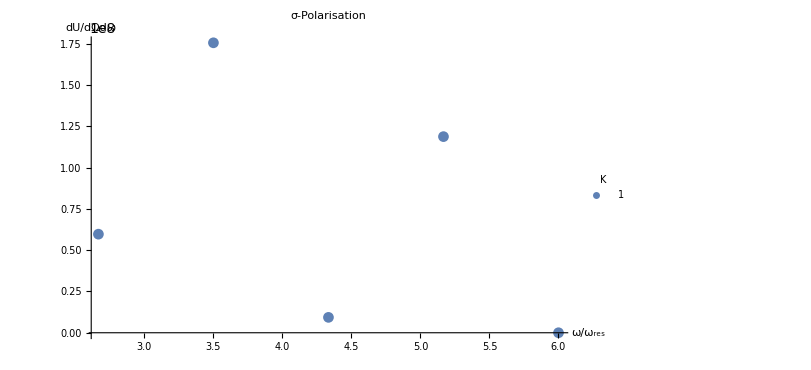

```mathematica
ListPlot[makeSRarc[0.,0.,{ωrange-> {1,6},ωpoints->6, logInterval->False}][[All,{1,4}]], PlotRange->{All,All}, ImageSize->600, AxesLabel->{"ω/ω_res","dU/dΩdω"}, PlotLegends->LineLegend[{1}, LegendLabel->"K"], PlotLabel->"σ-Polarisation"]
```

```mathematica
makeSRarc[0.,0.,{ωrange->{1,5},ωpoints->6}]
```

{{5^(1/5),0.,0.,3.24831×10^8},{5^(2/5),0.,0.,3.19638×10^6},{5^(3/5),0.,0.,4.34862×10^7},{5^(4/5),0.,0.,1.01238×10^8},{5,0.,0.,7.56735×10^7}}